#### Q4 a) (f,g) = ∫_0^1 f(x)g(x)ⅆx Basis for P_4 is {1,x,x^2, x^3,x^4}

Let N_1= 1, N_2= x, N_3= x^2, N_4= x^3, N_5= x^4. 
∴ f  =  ∑_(i=1)^5 N_i f_i
∴ (∫_0)^1(∑_(i=1)^5 N_i f_i)N_(1;;5)ⅆx = ∫_0^1 ⅇ^x N_(1;;5)ⅆx

```mathematica
(* Basis for equation *)
n = {{1,x,x^2, x^3,x^4},{1,Sin[π x],Cos[π x],Sin[2π x],Cos[2π x]}};

(* Unknnown coefficients Subscript[N, i] *) 
f = {f1,f2,f3,f4,f5};

(* Clear previous stored value *)
Clear[j];

(* Inititialize the value of j *)
j = 1;

(* Consider the basis {1, x,x^2, x^3,x^4} for equation (f,g) = ∫_0^1 f(x)g(x)ⅆx *)
Print[Style["For the basis {1, x,x^2, x^3,x^4}",Bold]];

(* Loop #1: Solve ∫_0^1 (Subscript[N, i](x).Subscript[f, i])Subscript[N, i] ⅆx for i = 1 to 6 *)
While[j<6,
	Print[Integrate[(∑_(i=1)^5 n[[1,i]]*f[[i]])*n[[1,j]],{x,0,1}]," = ",Integrate[E^x*n[[1,j]],{x,0,1}]];
	j = j+1;
(* Loop #1: End *)
]

(* Clear the memory of variables *)
Clear[l,m]; 
l = 1;

(* Initialize null matrix *)
Nmatrix1 = {}; 

(* Creating the list of elements for Matrix *)
(* Loop #2: Start the loop for row *)
While[l<6,
	m = 1;
	
(* Loop #3: Start the loop for column *)
	While[m<6,

(* Add new element in List *)
		AppendTo[Nmatrix1,Integrate[n[[1,m]]*n[[1,l]],{x,0,1}]];
		m = m + 1;

(* Loop #3: End *)
	];
	l = l + 1;

(* Loop #2: End *)
]

(* Making matrix from list *)
Print[MatrixForm[Table[Nmatrix1[[p;;p+4]],{p,1,22,5}]]," . ",MatrixForm[ArrayReshape[f,{5,1}]] ," = ",MatrixForm[ArrayReshape[Table[Integrate[E^x*n[[1,j]],{x,0,1}],{j,1,5}],{5,1}]]]

(* Solving equation by Linearly *)
Print[MatrixForm[ArrayReshape[f,{5,1}]]," = ", MatrixForm[LinearSolve[N[Table[Nmatrix1[[p;;p+4]],{p,1,22,5}]],N[ArrayReshape[Table[Integrate[E^x*n[[1,j]],{x,0,1}],{j,1,5}],{5,1}]]]]]

(* Generating function *)
F1 = Total/@N[LinearSolve[N[Table[Nmatrix1[[p;;p+4]],{p,1,22,5}]],N[ArrayReshape[Table[Integrate[E^x*n[[1,j]],{x,0,1}],{j,1,5}],{5,1}]]]];
func1[x_] = ∑_(i=1)^5 n[[1,i]]*F1[[i]];
Print["∫_0^1 ⅇ^xⅆx ≈ ",func1[x]];
```

For the basis {1, x,x^2, x^3,x^4}

f1+f2/2+f3/3+f4/4+f5/5 = -1+ⅇ

f1/2+f2/3+f3/4+f4/5+f5/6 = 1

f1/3+f2/4+f3/5+f4/6+f5/7 = -2+ⅇ

f1/4+f2/5+f3/6+f4/7+f5/8 = 6-2 ⅇ

f1/5+f2/6+f3/7+f4/8+f5/9 = -24+9 ⅇ

(1 | 1/2 | 1/3 | 1/4 | 1/5
1/2 | 1/3 | 1/4 | 1/5 | 1/6
1/3 | 1/4 | 1/5 | 1/6 | 1/7
1/4 | 1/5 | 1/6 | 1/7 | 1/8
1/5 | 1/6 | 1/7 | 1/8 | 1/9) . (f1
f2
f3
f4
f5) = (-1+ⅇ
1
-2+ⅇ
6-2 ⅇ
-24+9 ⅇ)

(f1
f2
f3
f4
f5) = (1.00005
0.998448
0.510579
0.139663
0.0694811)

∫_0^1 ⅇ^xⅆx ≈ 1.00005+0.998448 x+0.510579 x^2+0.139663 x^3+0.0694811 x^4

#### Q4 c) (f,g) = ∫_0^1 f(x)g(x)ⅆx Basis for P_4 is {1,Sin[π x],Cos[π x],Sin[2π x],Cos[2π x]}

Let N_1= 1, N_2= Sin[πx], N_3= Cos[πx], N_4= Sin[2πx], N_5= Cos[2πx]. 
∴ f  =  ∑_(i=1)^5 N_i f_i
∴ (∫_0)^1(∑_(i=1)^5 N_i f_i)N_(1;;5)ⅆx = ∫_0^1 ⅇ^x N_(1;;5)ⅆx

```mathematica
(* Clear previous stored value *)
Clear[j];

(* Inititialize the value of j *)
j = 1;

(* Consider the basis {1,Sin[π x],Cos[π x],Sin[2π x],Cos[2π x]} for equation (f,g) = ∫_0^1 f(x)g(x)ⅆx *)
Print[Style["
For the Basis {1,Sin[π x],Cos[π x],Sin[2π x],Cos[2π x]}",Bold]];

(* Loop #1: Solve ∫_0^1 (Subscript[N, i](x).Subscript[f, i])Subscript[N, i] ⅆx for i = 1 to 6 *)
While[j<6,
	Print[Integrate[(∑_(i=1)^5 (n[[2,i]]*f[[i]]))*n[[2,j]],{x,0,1}]," = ",Integrate[E^x*n[[2,j]],{x,0,1}]];
	j = j+1;

(* Loop #1: End *)
]
(* Clear the memory of variables *)
Clear[l,m]; 
l = 1;

(* Initialize null matrix *)
Nmatrix2 = {}; 

(* Creating the list of elements for Matrix *)
(* Loop #2: Start the loop for row *)
While[l<6,
	m = 1;
	
(* Loop #3: Start the loop for column *)
	While[m<6,

(* Add new element in List *)
		AppendTo[Nmatrix2,Integrate[n[[2,m]]*n[[2,l]],{x,0,1}]];
		m = m + 1;

(* Loop #3: End *)
	];
	l = l + 1;

(* Loop #2: End *)
]

(* Making matrix from list *)
Print[MatrixForm[Table[Nmatrix2[[p;;p+4]],{p,1,22,5}]]," . ",MatrixForm[ArrayReshape[f,{5,1}]] ," = ",MatrixForm[ArrayReshape[Table[Integrate[E^x*n[[2,j]],{x,0,1}],{j,1,5}],{5,1}]]]

(* Solving equation by Linearly *)
Print[MatrixForm[ArrayReshape[f,{5,1}]]," = ", MatrixForm[LinearSolve[N[Table[Nmatrix2[[p;;p+4]],{p,1,22,5}]],N[ArrayReshape[Table[Integrate[E^x*n[[2,j]],{x,0,1}],{j,1,5}],{5,1}]]]]]

(* Generating function *)
F2 = Total/@N[LinearSolve[N[Table[Nmatrix2[[p;;p+4]],{p,1,22,5}]],N[ArrayReshape[Table[Integrate[E^x*n[[2,j]],{x,0,1}],{j,1,5}],{5,1}]]]];
func2[x_] = ∑_(i=1)^5 n[[1,i]]*F2[[i]];
Print["∫_0^1 ⅇ^xⅆx ≈ ",func2[x]];
```

For the Basis {1,Sin[π x],Cos[π x],Sin[2π x],Cos[2π x]}

f1+(2 f2)/π = -1+ⅇ

(12 f1-4 f5+3 f2 π)/(6 π) = ((1+ⅇ) π)/(1+π^2)

f3/2+(4 f4)/(3 π) = -(1+ⅇ)/(1+π^2)

f4/2+(4 f3)/(3 π) = -(2 (-1+ⅇ) π)/(1+4 π^2)

f5/2-(2 f2)/(3 π) = (-1+ⅇ)/(1+4 π^2)

(1 | 2/π | 0 | 0 | 0
2/π | 1/2 | 0 | 0 | -2/(3 π)
0 | 0 | 1/2 | 4/(3 π) | 0
0 | 0 | 4/(3 π) | 1/2 | 0
0 | -2/(3 π) | 0 | 0 | 1/2) . (f1
f2
f3
f4
f5) = (-1+ⅇ
((1+ⅇ) π)/(1+π^2)
-(1+ⅇ)/(1+π^2)
-(2 (-1+ⅇ) π)/(1+4 π^2)
(-1+ⅇ)/(1+4 π^2))

(f1
f2
f3
f4
f5) = (1.88222
-0.257509
-0.827813
0.169235
-0.0243917)

∫_0^1 ⅇ^xⅆx ≈ 1.88222-0.257509 x-0.827813 x^2+0.169235 x^3-0.0243917 x^4

#### Q4 b) (f,g) = ∫_0^1 (f(x)g(x))/(√(x(1-x)))ⅆx Basis for P_4 is {1, x,x^2, x^3,x^4}

Let N_1= 1, N_2= x, N_3= x^2, N_4= x^3, N_5= x^4. 
∴ f  =  ∑_(i=1)^5 N_i f_i
∴ (∫_0)^1((∑_(i=1)^5 N_i f_i)N_(1;;5))/(√(x(1-x)))ⅆx = ∫_0^1 (ⅇ^x N_(1;;5))/(√(x(1-x)))ⅆx

```mathematica
(* Clear previous stored value *)
Clear[j];

(* Inititialize the value of j *)
j = 1;

(* Consider the basis {1, x,x^2, x^3,x^4} for equation (f,g) = ∫_0^1 (f(x)g(x))/(√(x(1-x)))ⅆx *)
Print[Style["For the basis {1, x,x^2, x^3,x^4}",Bold]];

(* Loop #1: Solve ∫_0^1 ((Subscript[N, i](x).Subscript[f, i])Subscript[N, i])/(√(x*(1-x)))ⅆx for i = 1 to 6 *)
While[j<6,
Print[Integrate[∑_(i=1)^5 (1.0*n[[1,i]]*f[[i]]*n[[1,j]])/(√(x*(1-x))),{x,0,1}]," = ",NIntegrate[E^x*n[[1,j]]/(√(x*(1-x))),{x,0,1}]];
j = j+1;

(* Loop #1: End *)
]

(* Clear the memory of variables *)
Clear[l,m]; 
l = 1;

(* Initialize null matrix *)
Nmatrix3 = {}; 

(* Creating the list of elements for Matrix *)
(* Loop #2: Start the loop for row *)
While[l<6,
	m = 1;
	
(* Loop #3: Start the loop for column *)
	While[m<6,

(* Add new element in List *)
		AppendTo[Nmatrix3,NIntegrate[n[[1,m]]*n[[1,l]]/(√(x*(1-x))),{x,0,1}]];
		m = m + 1;

(* Loop #3: End *)
	];
	l = l + 1;

(* Loop #2: End *)
]

(* Making matrix from list *)
Print[MatrixForm[Table[Nmatrix3[[p;;p+4]],{p,1,22,5}]]," . ",MatrixForm[ArrayReshape[f,{5,1}]] ," = ",MatrixForm[ArrayReshape[Table[NIntegrate[E^x*n[[1,j]]/(√(x*(1-x))),{x,0,1}],{j,1,5}],{5,1}]]]

(* Solving equation by Linearly *)
Print[MatrixForm[ArrayReshape[f,{5,1}]]," = ", MatrixForm[LinearSolve[N[Table[Nmatrix3[[p;;p+4]],{p,1,22,5}]],N[ArrayReshape[Table[NIntegrate[E^x*n[[1,j]]/(√(x*(1-x))),{x,0,1}],{j,1,5}],{5,1}]]]]]

(* Generating function *)
F1 = Total/@N[LinearSolve[N[Table[Nmatrix3[[p;;p+4]],{p,1,22,5}]],N[ArrayReshape[Table[NIntegrate[E^x*n[[1,j]]/(√(x*(1-x))),{x,0,1}],{j,1,5}],{5,1}]]]];
func3[x_] = ∑_(i=1)^5 n[[1,i]]*F1[[i]];
Print["∫_0^1 ⅇ^xⅆx ≈ ",func3[x]];
```

For the basis {1, x,x^2, x^3,x^4}

3.14159 f1+1.5708 f2+1.1781 f3+0.981748 f4+0.859029 f5 = 5.50843

1.5708 f1+1.1781 f2+0.981748 f3+0.859029 f4+0.773126 f5 = 3.42211

1.1781 f1+0.981748 f2+0.859029 f3+0.773126 f4+0.708699 f5 = 2.75421

0.981748 f1+0.859029 f2+0.773126 f3+0.708699 f4+0.658078 f5 = 2.37895

0.859029 f1+0.773126 f2+0.708699 f3+0.658078 f4+0.616948 f5 = 2.12763

(3.14159 | 1.5708 | 1.1781 | 0.981748 | 0.859029
1.5708 | 1.1781 | 0.981748 | 0.859029 | 0.773126
1.1781 | 0.981748 | 0.859029 | 0.773126 | 0.708699
0.981748 | 0.859029 | 0.773126 | 0.708699 | 0.658078
0.859029 | 0.773126 | 0.708699 | 0.658078 | 0.616948) . (f1
f2
f3
f4
f5) = (5.50843
3.42211
2.75421
2.37895
2.12763)

(f1
f2
f3
f4
f5) = (1.00003
0.998724
0.509949
0.140001
0.0695536)

∫_0^1 ⅇ^xⅆx ≈ 1.00003+0.998724 x+0.509949 x^2+0.140001 x^3+0.0695536 x^4

#### Q4 d) (f,g) = ∫_0^1 (f(x)g(x))/(√(x(1-x)))ⅆx Basis for P_4 is {1,Sin[π x],Cos[π x],Sin[2π x],Cos[2π x]}

Let N_1= 1, N_2= Sin[πx], N_3= Cos[πx], N_4= Sin[2πx], N_5= Cos[2πx].
∴ f  =  ∑_(i=1)^5 N_i f_i
∴ (∫_0)^1((∑_(i=1)^5 N_i f_i)N_(1;;5))/(√(x(1-x)))ⅆx = ∫_0^1 (ⅇ^x N_(1;;5))/(√(x(1-x)))ⅆx

```mathematica
(* Clear previous stored value *)
Clear[j];

(* Inititialize the value of j *)
j = 1;

(* Consider the basis {1,Sin[π x],Cos[π x],Sin[2π x],Cos[2π x]} for equation (f,g) = ∫_0^1 (f(x)g(x))/(√(x(1-x)))ⅆx *)
Print[Style["
For the Basis {1,Sin[π x],Cos[π x],Sin[2π x],Cos[2π x]}",Bold]];

(* Loop #1: Solve ∫_0^1 ((Subscript[N, i](x).Subscript[f, i])Subscript[N, i])/(√(x*(1-x)))ⅆx for i = 1 to 6 *)
While[j<6,
	Print[Integrate[∑_(i=1)^5 (1.0*n[[2,i]]*f[[i]]*n[[2,j]])/(√(x*(1-x))),{x,0,1}]," = ",NIntegrate[E^x*n[[2,j]]/(√(x*(1-x))),{x,0,1.}]];
	j = j+1;

(* Loop #1: End *)
]
(* Clear the memory of variables *)
Clear[l,m]; 
l = 1;

(* Initialize null matrix *)
Nmatrix4 = {}; 

(* Creating the list of elements for Matrix *)
(* Loop #2: Start the loop for row *)
While[l<6,
	m = 1;
	
(* Loop #3: Start the loop for column *)
	While[m<6,

(* Add new element in List *)
		AppendTo[Nmatrix4,NIntegrate[n[[2,m]]*n[[2,l]]/(√(x*(1-x))),{x,0,1}]];
		m = m + 1;

(* Loop #3: End *)
	];
	l = l + 1;

(* Loop #2: End *)
]

(* Making matrix from list *)
Print[MatrixForm[Table[Nmatrix4[[p;;p+4]],{p,1,22,5}]]," . ",MatrixForm[ArrayReshape[f,{5,1}]] ," = ",MatrixForm[ArrayReshape[Table[NIntegrate[E^x*n[[2,j]]/(√(x*(1-x))),{x,0,1}],{j,1,5}],{5,1}]]]

(* Solving equation by Linearly *)
Print[MatrixForm[ArrayReshape[f,{5,1}]]," = ", MatrixForm[LinearSolve[N[Table[Nmatrix4[[p;;p+4]],{p,1,22,5}]],N[ArrayReshape[Table[NIntegrate[E^x*n[[2,j]]/(√(x*(1-x))),{x,0,1}],{j,1,5}],{5,1}]]]]]

(* Generating function *)
F2 = Total/@N[LinearSolve[N[Table[Nmatrix4[[p;;p+4]],{p,1,22,5}]],N[ArrayReshape[Table[NIntegrate[E^x*n[[2,j]]/(√(x*(1-x))),{x,0,1}],{j,1,5}],{5,1}]]]];
func4[x_] = ∑_(i=1)^5 n[[1,i]]*F2[[i]];
Print["∫_0^1 ⅇ^xⅆx ≈ ",func4[x]];
```

For the Basis {1,Sin[π x],Cos[π x],Sin[2π x],Cos[2π x]}

3.14159 f1+1.48284 f2+0.955805 f5 = 5.50843

1.48284 f1+1.09289 f2-0.32381 f5 = 2.51748

2.0487 f3+1.15903 f4 = -1.51243

1.15903 f3+1.22479 f4 = -0.751241

0.955805 f1-0.32381 f2+1.91681 f5 = 1.83609

(3.14159 | 1.48284 | 2.13024×10^-15 | 3.90313×10^-18 | 0.955805
1.48284 | 1.09289 | 1.95156×10^-18 | -5.20417×10^-18 | -0.32381
2.13024×10^-15 | 1.95156×10^-18 | 2.0487 | 1.15903 | 2.14585×10^-15
3.90313×10^-18 | -5.20417×10^-18 | 1.15903 | 1.22479 | -1.07336×10^-16
0.955805 | -0.32381 | 2.14585×10^-15 | -1.07336×10^-16 | 1.91681) . (f1
f2
f3
f4
f5) = (5.50843
2.51748
-1.51243
-0.751241
1.83609)

(f1
f2
f3
f4
f5) = (1.88417
-0.260538
-0.842019
0.183445
-0.0256553)

∫_0^1 ⅇ^xⅆx ≈ 1.88417-0.260538 x-0.842019 x^2+0.183445 x^3-0.0256553 x^4

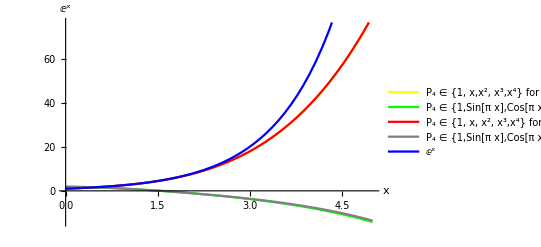

```mathematica
(* Plot all for approximation *)
Plot[{func1[x],func2[x],func3[x],func4[x],E^x},{x,0,5},PlotLegends->{"P_4 ∈ {1, x,x^2, x^3,x^4} for Part a",
"P_4 ∈ {1,Sin[π x],Cos[π x],Sin[2π x],Cos[2π x]} for Part a","P_4 ∈ {1, x, x^2, x^3,x^4} for Part b",
"P_4 ∈ {1,Sin[π x],Cos[π x],Sin[2π x],Cos[2π x]} for Part b","ⅇ^x"},PlotStyle->{Yellow,Green,Red,Gray,Blue},AxesLabel->{x,ⅇ^x}]
```

From the graph we can see that  basis  {1, x,x^2, x^3,x^4} is better than the basis  {1,Sin[π x],Cos[π x],Sin[2π x],Cos[2π x]}

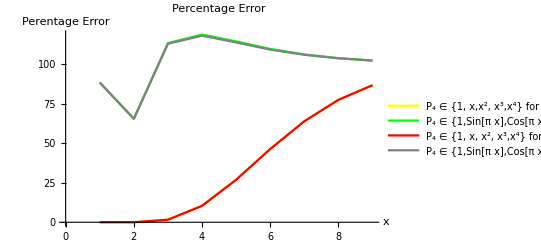

```mathematica
(* Percentage Error *)
i = 1;
err1 = {};
err2 = {};
err3 = {};
err4 = {};
While[i<10,
AppendTo[err1, Abs[(E^(i-1)- func1[i-1])/E^(i-1)]*100.];
AppendTo[err2, Abs[(E^(i-1)- func2[i-1])/E^(i-1)]*100.];
AppendTo[err3, Abs[(E^(i-1)- func3[i-1])/E^(i-1)]*100.];
AppendTo[err4, Abs[(E^(i-1)- func4[i-1])/E^(i-1)]*100.];


i = i+1;
]
ListLinePlot[{err1,err2,err3,err4},PlotLegends->{"P_4 ∈ {1, x,x^2, x^3,x^4} for Part a",
"P_4 ∈ {1,Sin[π x],Cos[π x],Sin[2π x],Cos[2π x]} for Part a","P_4 ∈ {1, x, x^2, x^3,x^4} for Part b",
"P_4 ∈ {1,Sin[π x],Cos[π x],Sin[2π x],Cos[2π x]} for Part b","ⅇ^x"},PlotStyle->{Yellow,Green,Red,Gray,Blue},PlotLabel->"Percentage Error",AxesLabel->{x,"Perentage Error"}]
```